```mathematica
<<NFPackages`structuralAnalysis`shearWalls`
```

```mathematica
?*esponse*
```

responseSpectrumAccelerationEurocodeElastic2004[ periodOfSDOF ] returns the acceleration in m/s^2 (meters per second per second).  accelerationResponseSpectrumFunction[] returns a grid depiction of the defaults used in options.  Options allow customizing the spectrum function including setting up some reference magnitude for the acceleration (see Options[ accelerationResponseSpectrumFunction ]).

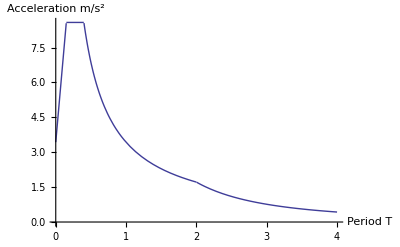

```mathematica
Plot[ responseSpectrumAccelerationEurocodeElastic2004[ T], {T, 0, 4}, PlotRange -> {{0, 4}, {0, Automatic}},
AxesLabel -> {"Period T", "Acceleration m/s^2"} ]
```